### α

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
Clear[ΛQCD];
Clear[LQ];
Clear[αsNf];
Clear[Mαs];
Clear[αs];
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

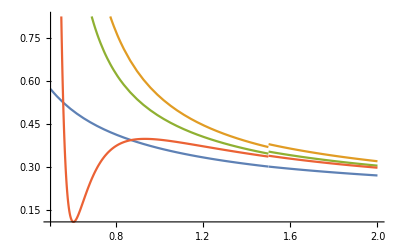

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

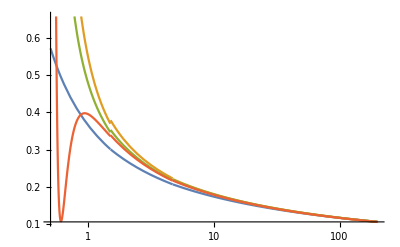

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
Nf4α1LoopMid=Table[αs1Loop[Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopStepTab=Round[4/(.2 Nf4α1LoopMid^2)]
```

{430,411,390,367,342,314,282,245}

```mathematica
Nf4α1LoopBig=Table[αs1Loop[1/2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.268835,0.276665,0.28589,0.296997,0.311546,0.330832,0.357283,0.396841}

```mathematica
Nf4α1LoopSmall=Table[αs1Loop[2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.181799,0.185058,0.188807,0.193197,0.198453,0.204935,0.213849,0.226354}

```mathematica
Length[DeleteDuplicates[Join[Nf4α1LoopMid,Nf4α1LoopBig,Nf4α1LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α1Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.1266,72.9651,62.6156,52.0329,41.1465,29.8326,17.822,4.05254}

```mathematica
Mt
```

173.34

```mathematica
Nf5α1LoopMid=Table[αs1Loop[Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopStepTab=Round[4/(.2 Nf5α1LoopMid^2)]
```

{1391,1339,1278,1207,1120,1006,835,430}

```mathematica
Nf5α1LoopBig=Table[αs1Loop[1/2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.133418,0.136311,0.13987,0.144434,0.150667,0.160132,0.178055,0.268835}

```mathematica
Nf5α1LoopSmall=Table[αs1Loop[2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.108852,0.11077,0.113109,0.116075,0.120067,0.126002,0.136841,0.181799}

```mathematica
Length[DeleteDuplicates[Join[Nf5α1LoopMid,Nf5α1LoopBig,Nf5α1LoopSmall]]]
```

24

```mathematica
Nf4α1LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α1LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α2Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α2LoopMid=Table[αs2Loop[Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopStepTab=Round[4/(.2 Nf4α2LoopMid^2)]
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf4α2LoopBig=Table[αs2Loop[1/2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall=Table[αs2Loop[2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.223621,0.238097}

```mathematica
Nf4α2LoopSmall[[-2]]=0.22362;
```

```mathematica
Length[DeleteDuplicates[Join[Nf4α2LoopMid,Nf4α2LoopBig,Nf4α2LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α2Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α2Loopμ/Nf5mQTab
```

{0.481523,0.491366,0.50345,0.518914,0.539976,0.571839,0.631796,0.917683}

```mathematica
2Nf5α2Loopμ/Nf5mQTab
```

{0.963046,0.982731,1.0069,1.03783,1.07995,1.14368,1.26359,1.83537}

```mathematica
1/2Nf5α2Loopμ/Nf5mQTab
```

{0.240762,0.245683,0.251725,0.259457,0.269988,0.285919,0.315898,0.458842}

```mathematica
Nf5α2LoopMid=Table[αs2Loop[Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopStepTab=Round[4/(.2 Nf5α2LoopMid^2)]
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α2LoopBig=Table[αs2Loop[1/2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall=Table[αs2Loop[2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Length[DeleteDuplicates[Join[Nf5α2LoopMid,Nf5α2LoopBig,Nf5α2LoopSmall]]]
```

24

```mathematica
Nf4α2LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α2LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NNLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α3Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf4α3LoopMid=Table[αs3Loop[Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopStepTab=Round[4/(.2 Nf4α3LoopMid^2)]
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α3LoopBig=Table[αs3Loop[1/2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall=Table[αs3Loop[2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Length[DeleteDuplicates[Join[Nf4α3LoopMid,Nf4α3LoopBig,Nf4α3LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α3Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α3Loopμ/Nf5mQTab
```

{0.481536,0.491353,0.503401,0.518811,0.539782,0.571469,0.630948,0.902505}

```mathematica
2Nf5α3Loopμ/Nf5mQTab
```

{0.963073,0.982706,1.0068,1.03762,1.07956,1.14294,1.2619,1.80501}

```mathematica
1/2Nf5α3Loopμ/Nf5mQTab
```

{0.240768,0.245677,0.251701,0.259405,0.269891,0.285734,0.315474,0.451253}

```mathematica
Nf5α3LoopMid=Table[αs3Loop[Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopStepTab=Round[4/(.2 Nf5α3LoopMid^2)]
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf5α3LoopBig=Table[αs3Loop[1/2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall=Table[αs3Loop[2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Length[DeleteDuplicates[Join[Nf5α3LoopMid,Nf5α3LoopBig,Nf5α3LoopSmall]]]
```

24

```mathematica
Nf4α3LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α3LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

## baryons

```mathematica
4 .214850
```

0.8594

```mathematica
αs1Loop[0.8594 4.77041]
```

0.21485

```mathematica
4 0.227325
```

0.9093

```mathematica
αs2Loop[0.9093 4.86831]
```

0.227325

```mathematica
4 0.313613
```

1.25445

```mathematica
αs3Loop[0.889968 4.96974]
```

0.222492

```mathematica
4 0.282678
```

1.13071

```mathematica
αs1Loop[1.130712 1.56206]
```

0.282678

```mathematica
4 0.313613
```

1.25445

```mathematica
αs2Loop[1.254452 1.65234]
```

0.313791

```mathematica
mu2Loop[mQ_?NumericQ]:=mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}]
```

```mathematica
sol2Loop=FindRoot[αs2Loop[mu2Loop]==0.313613,{mu2Loop,1.254452}]
```

{mu2Loop→2.07503}

```mathematica
mu2=mu2Loop/.sol2Loop[[1]]
```

2.07503

```mathematica
sol2LoopP=FindRoot[mu2Loop[mQ]==mu2,{mQ,1.65234}]
```

{mQ→1.65413}

```mathematica
mQ2=mQ/.sol2LoopP[[1]]
```

1.65413

```mathematica
mu2/mQ2
```

1.25445

```mathematica
4 .297100
```

1.1884

```mathematica
αs3Loop[1.1884 1.77092]
```

0.297152

```mathematica
mu3Loop[mQ_?NumericQ]:=mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}]
```

```mathematica
sol3Loop=FindRoot[αs3Loop[mu3Loop]==.297100,{mu3Loop,1.1884}]
```

{mu3Loop→2.10536}

```mathematica
mu3=mu3Loop/.sol3Loop[[1]]
```

2.10536

```mathematica
sol3LoopP=FindRoot[mu3Loop[mQ]==mu3,{mQ,1.65234}]
```

{mQ→1.77159}

```mathematica
mQ3=mQ/.sol3LoopP[[1]]
```

1.77159

```mathematica
mu3/mQ3
```

1.1884

```mathematica
1.771737016610082/1.2943483126744015
```

```mathematica
fudge=4;
```

```mathematica
mbmb=4.77041;
```

```mathematica
mcmc=1.56206;
```

```mathematica
Mbbarexp=9.44295;
```

```mathematica
Mccbarexp=3.06865;
```

```mathematica
mu[mQ_?NumericQ]:=mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]
```

```mathematica
mredbbc=3mbmb mcmc/(2mbmb+mcmc)
```

2.01344

```mathematica
mubbc=mu[mredbbc]
```

2.12797

```mathematica
αs1Loop[mubbc]
```

0.264221

```mathematica
mubbc/mredbbc
```

1.05688

```mathematica
4αs1Loop[mubbc]
```

1.05688

```mathematica
(3-0.03281064)mredbbc
```

5.97426

```mathematica
SetPrecision[2mbmb+mcmc-0.03281064mredbbc,10]
```

11.03681769

```mathematica
1.4538*10^(-5)mredbbc
```

0.0000292714

```mathematica
mbmb2Loop=4.86831;
```

```mathematica
mcmc2Loop=1.65413;
```

```mathematica
mredbbc2Loop=3mbmb2Loop mcmc2Loop/(2mbmb2Loop+mcmc2Loop)
```

2.12088

```mathematica
mubbc2Loop=mu2Loop[mredbbc2Loop]
```

2.45011

```mathematica
αs2Loop[mubbc2Loop]
```

0.288808

```mathematica
mubbc2Loop/mredbbc2Loop
```

1.15523

```mathematica
4 αs2Loop[mubbc2Loop]
```

1.15523

```mathematica
mbmb3Loop=4.96974;
```

```mathematica
mcmc3Loop=1.77159;
```

```mathematica
mredbbc3Loop=3mbmb3Loop mcmc3Loop/(2mbmb3Loop+mcmc3Loop)
```

2.25539

```mathematica
mubbc3Loop=mu3Loop[mredbbc3Loop]
```

2.48883

```mathematica
αs3Loop[mubbc3Loop]
```

0.275876

```mathematica
mubbc3Loop/mredbbc3Loop
```

1.1035

```mathematica
4 αs3Loop[mubbc3Loop]
```

1.1035

```mathematica
mredbcc=3mbmb mcmc/(mbmb+2mcmc)
```

2.83171

```mathematica
mubcc=mu[mredbcc]
```

2.74699

```mathematica
αs1Loop[mubcc]
```

0.242521

```mathematica
mubcc/mredbcc
```

0.970083

```mathematica
4αs1Loop[mubcc]
```

0.970083

```mathematica
mredbcc2Loop=3mbmb2Loop mcmc2Loop/(mbmb2Loop+2mcmc2Loop)
```

2.9546

```mathematica
mubcc2Loop=mu2Loop[mredbcc2Loop]
```

3.08353

```mathematica
αs2Loop[mubcc2Loop]
```

0.26091

```mathematica
mubcc2Loop/mredbcc2Loop
```

1.04364

```mathematica
4 αs2Loop[mubcc2Loop]
```

1.04364

```mathematica
mredbcc3Loop=3mbmb3Loop mcmc3Loop/(mbmb3Loop+2mcmc3Loop)
```

3.1027

```mathematica
mubcc3Loop=mu3Loop[mredbcc3Loop]
```

3.12451

```mathematica
αs3Loop[mubcc3Loop]
```

0.251758

```mathematica
mubcc3Loop/mredbcc3Loop
```

1.00703

```mathematica
4 αs3Loop[mubcc3Loop]
```

1.00703

## bc meson

### 1 Loop

```mathematica
mredbc=2mbmb mcmc/(mbmb+mcmc)
```

2.35348

```mathematica
mubc=mu[mredbc]
```

2.39007

```mathematica
αs1Loop[mubc]
```

0.253887

```mathematica
eqqbarmubc=-(4/3 αs1Loop[mubc])^2/4
```

-0.0286483

```mathematica
Mbc = mbmb+mcmc+eqqbarmubc mredbc
```

6.26505

```mathematica
(* alternative scheme *)
```

```mathematica
mbmubc=Mbbarexp/(eqqbarmubc+2)
```

4.79009

```mathematica
mcmubc=Mccbarexp/(eqqbarmubc+2)
```

1.55662

```mathematica
Mrun=2mbmubc mcmubc/(mbmubc+mcmubc)
```

2.34968

```mathematica
muRun=mubc/Mrun
```

1.01719

```mathematica
4αs1Loop[mubc]
```

1.01555

```mathematica
mbmubc+mcmubc+eqqbarmubc Mrun
```

6.2794

### 2 Loop

```mathematica
mredbc2Loop=2mbmb2Loop mcmc2Loop/(mbmb2Loop+mcmc2Loop)
```

2.46927

```mathematica
mubc2Loop=mu2Loop[mredbc2Loop]
```

2.71967

```mathematica
αs2Loop[mubc2Loop]
```

0.275353

```mathematica
4αs2Loop[mubc2Loop]
```

1.10141

```mathematica
4αs2Loop[mubc2Loop]==mubc2Loop/mredbc2Loop
```

True

```mathematica
eqqbarmubc2Loop=
```

```mathematica
Mbc = mbmb+mcmc+eqqbarmubc mredbc
```

```mathematica
(*mbmubc2Loop=Mbbarexp/(eqqbarmubc2Loop+2)*)
```

```mathematica
(*mcmubc2Loop=Mccbarexp/(eqqbarmubc2Loop+2)*)
```

```mathematica
(*Mrun2Loop=2mbmubc2Loop mcmubc2Loop/(mbmubc2Loop+mcmubc2Loop)*)
```

```mathematica
(*mbmubc2Loop+mcmubc2Loop+eqqbarmubc2Loop Mrun2Loop*)
```

### 3 Loop

```mathematica
mredbc3Loop=2mbmb3Loop mcmc3Loop/(mbmb3Loop+mcmc3Loop)
```

2.61205

```mathematica
mubc3Loop=mu3Loop[mredbc3Loop]
```

2.76118

```mathematica
αs3Loop[mubc3Loop]
```

0.264274

```mathematica
4αs3Loop[mubc3Loop]
```

1.05709

```mathematica
4αs3Loop[mubc3Loop]==mubc3Loop/mredbc3Loop
```

True

```mathematica
eqqbarmubc3Loop=
```

```mathematica
Mbc = mbmb+mcmc+eqqbarmubc mredbc
```

```mathematica
(*mbmubc3Loop=Mbbarexp/(eqqbarmubc3Loop+2)*)
```

```mathematica
(*mcmubc3Loop=Mccbarexp/(eqqbarmubc3Loop+2)*)
```

```mathematica
(*Mrun3Loop=2mbmubc3Loop mcmubc3Loop/(mbmubc3Loop+mcmubc3Loop)*)
```

```mathematica
(*mbmubc3Loop+mcmubc3Loop+eqqbarmubc3Loop Mrun3Loop*)
```

## Tetraquarks

### bbcc

```mathematica
mredbbcc=4mbmb mcmc/(2mbmb+2mcmc)
```

2.35348

```mathematica
mubbcc=mu[mredbbcc]
```

2.39007

```mathematica
αs1Loop[mubbcc]
```

0.253887

```mathematica
mredbbcc2Loop=4mbmb2Loop mcmc2Loop/(2mbmb2Loop+2mcmc2Loop)
```

2.46927

```mathematica
mubbcc2Loop=mu2Loop[mredbbcc2Loop]
```

2.71967

```mathematica
αs2Loop[mubbcc2Loop]
```

0.275353

```mathematica
4αs2Loop[mubbcc2Loop]
```

1.10141

```mathematica
4αs2Loop[mubbcc2Loop]==mubbcc2Loop/mredbbcc2Loop
```

True

```mathematica
mredbbcc3Loop=4mbmb3Loop mcmc3Loop/(2mbmb3Loop+2mcmc3Loop)
```

2.61205

```mathematica
mubbcc3Loop=mu3Loop[mredbbcc3Loop]
```

2.76118

```mathematica
αs3Loop[mubbcc3Loop]
```

0.264274

```mathematica
4αs3Loop[mubbcc3Loop]
```

1.05709

```mathematica
4αs3Loop[mubbcc3Loop]==mubbcc3Loop/mredbbcc3Loop
```

True

### bbbc

```mathematica
mredbbbc=4mbmb mcmc/(3mbmb+1mcmc)
```

1.87779

```mathematica
mubbbc=mu[mredbbbc]
```

2.0211

```mathematica
αs1Loop[mubbbc]
```

0.26908

```mathematica
mredbbbc2Loop=4mbmb2Loop mcmc2Loop/(3mbmb2Loop+1mcmc2Loop)
```

1.98113

```mathematica
mubbbc2Loop=mu2Loop[mredbbbc2Loop]
```

2.33965

```mathematica
αs2Loop[mubbbc2Loop]
```

0.295242

```mathematica
4αs2Loop[mubbbc2Loop]
```

1.18097

```mathematica
4αs2Loop[mubbbc2Loop]==mubbbc2Loop/mredbbbc2Loop
```

True

```mathematica
mredbbbc3Loop=4mbmb3Loop mcmc3Loop/(3mbmb3Loop+1mcmc3Loop)
```

2.11125

```mathematica
mubbbc3Loop=mu3Loop[mredbbbc3Loop]
```

2.37644

```mathematica
αs3Loop[mubbbc3Loop]
```

0.281402

```mathematica
4αs3Loop[mubbbc3Loop]
```

1.12561

```mathematica
4αs3Loop[mubbbc3Loop]==mubbbc3Loop/mredbbbc3Loop
```

True

### bccc

```mathematica
mredbccc=4mbmb mcmc/(1mbmb+3mcmc)
```

3.15195

```mathematica
mubccc=mu[mredbccc]
```

2.97971

```mathematica
αs1Loop[mubccc]
```

0.236339

```mathematica
mredbccc2Loop=4mbmb2Loop mcmc2Loop/(1mbmb2Loop+3mcmc2Loop)
```

3.2766

```mathematica
mubccc2Loop=mu2Loop[mredbccc2Loop]
```

3.3187

```mathematica
αs2Loop[mubccc2Loop]
```

0.253212

```mathematica
4αs2Loop[mubccc2Loop]
```

1.01285

```mathematica
4αs2Loop[mubccc2Loop]==mubccc2Loop/mredbccc2Loop
```

True

```mathematica
mredbccc3Loop=4mbmb3Loop mcmc3Loop/(1mbmb3Loop+3mcmc3Loop)
```

3.42431

```mathematica
mubccc3Loop=mu3Loop[mredbccc3Loop]
```

3.35671

```mathematica
αs3Loop[mubccc3Loop]
```

0.245064

```mathematica
4αs3Loop[mubccc3Loop]
```

0.980258

```mathematica
4αs3Loop[mubccc3Loop]==mubccc3Loop/mredbccc3Loop
```

True

### old

```mathematica
ΔEbbccLO=-(4/3 αs1Loop[mubbcc])^2/4
```

```mathematica
mbmubbcc=Mbbarexp/(ΔEbbccLO+2)
```

```mathematica
mcmubbcc=Mccbarexp/(ΔEbbccLO+2)
```

```mathematica
mBc=mbmubbcc+mcmubbcc+(2 mbmubbcc mcmubbcc/(mbmubbcc+mcmubbcc)) ΔEbbccLO
```

```mathematica
SetPrecision[mBc,6]
```

```mathematica
mu[mbmb]
```

4.09969

```mathematica
αs1Loop[mu[mbmb]]
```

0.21485

```mathematica
αs1Loop[mu[mcmc]]
```

0.282678

```mathematica
2mbmb-(4/3 αs1Loop[mu[mbmb]])^2/4mbmb
```

9.44295

```mathematica
2mcmc-(4/3 αs1Loop[mu[mcmc]])^2/4mcmc
```

3.06864

```mathematica
mbmb
```

4.77041

```mathematica
mcmc
```

1.56206

```mathematica
mbbcc=2 mbmb mcmc/(mbmb+mcmc)
```

2.35348

```mathematica
mubbcc=mu[mbbcc]
```

2.39007

```mathematica
αs1Loop[mubbcc]
```

0.253887

```mathematica
ΔEbbccLO=-(4/3 αs1Loop[mubbcc])^2/4
```

-0.0286483

```mathematica
mbmubbcc=Mbbarexp/(ΔEbbccLO+2)
```

4.79009

```mathematica
mcmubbcc=Mccbarexp/(ΔEbbccLO+2)
```

1.55662

```mathematica
mubbcc/mbbcc
```

1.01555

```mathematica
mbmubbcc/mbbcc
```

2.03532

```mathematica
mcmubbcc/mbbcc
```

0.661413

```mathematica
mbbcc ΔEbbccLO
```

-0.0674231

```mathematica
mBc=mbmubbcc+mcmubbcc+(2 mbmubbcc mcmubbcc/(mbmubbcc+mcmubbcc)) ΔEbbccLO
```

6.2794

```mathematica
SetPrecision[mBc,6]
```

6.2794

```mathematica
mubbcc/mbbcc
```

1.01555

```mathematica
mcmubbcc/mbmubbcc
```

0.324967

```mathematica
Mrunat=2 mbmubbcc mcmubbcc/(mbmubbcc+mcmubbcc)
```

2.34968

```mathematica
mbmubbcc/mbbcc(mbbcc/Mrunat)
```

2.03862

```mathematica
mcmubbcc/mbbcc(mbbcc/Mrunat)
```

0.662484

```mathematica
mubbcc/mbbcc(mbbcc/Mrunat)
```

1.01719

```mathematica
mubbcc/mbbcc==4αs1Loop[mubbcc]
```

True

```mathematica
mubbcc/Mrunat==4αs1Loop[mubbcc](mbbcc/Mrunat)
```

True